```mathematica
f[x_]:=(Cos[x])^2;
Subscript[x, 0]=0;
Subscript[x, 1]=π/4;
Subscript[x, 2]=π/2;
n=2;
m=2;
NN=(m+1)(n+1)-1;
P[x_]=∑_(k=0)^NN Subscript[a, k] x^k;
eqv=Table[(D[P[x],{x,j}]//.x->Subscript[x, k])==(D[f[x],{x,j}]//.x->Subscript[x, k]),{j,0,m},{k,0,n}]//Flatten;
koef=Solve[eqv,{}]//Flatten ;
P[x_]=P[x]//.koef //N

Table[(D[P[x],{x,j}]//.x->Subscript[x, k])-(D[f[x],{x,j}]//.x->Subscript[x, k]),{j,0,m},{k,0,n}]//Flatten
```

1.-1. x^2+0.333332 x^4+0.0000100226 x^5-0.0444834 x^6+0.0000871359 x^7+0.00305176 x^8+0.000112837 x^9-0.000208012 x^10+0.0000240772 x^11

{0.,1.86517×10^-14,2.23377×10^-13,0.,1.21236×10^-13,5.2458×10^-13,0.,5.38056×10^-13,3.99902×10^-12,0.,8.41993×10^-13,4.31744×10^-11}

```mathematica
eq1=Table[P[Subscript[x, k]]==f[Subscript[x, k]],{k,0,n}];
PP[t_]=D[P[t], t];ff[t_]=D[f[t], t];eq2=Table[PP[Subscript[x, k]]==ff[Subscript[x, k]],{k,0,n}];PPP[t_]=D[PP[t], t];fff[t_]=D[ff[t], t];eq3=Table[PPP[Subscript[x, k]]==fff[Subscript[x, k]],{k,0,n}];
Tbl=Table[{Subscript[x, k],f[Subscript[x, k]],ff[Subscript[x, k]],fff[Subscript[x, k]]},{k,0,n}];
P1[x_]=InterpolatingPolynomial[Tbl,x]//Expand //N
P[x]-P1[x];
```

1.-1. x^2+0.0012104 x^3+0.326468 x^4+0.0157463 x^5-0.0629494 x^6+0.01145 x^7

```mathematica
(*Subscript[x, 0]=0;
Subscript[x, 1]=π/4;
Subscript[x, 2]=π/2;
n=2;
m=3;
NN=(m+1)(n+1)-1;
Pf[x_]=∑_(k=0)^NN Subscript[b, k] x^k;
eqv1:=Table[(D[Pf[x],{x,j}]//.x->Subscript[x, k])==(D[g[x],{x,j}]//.x->Subscript[x, k]),{j,0,m},{k,0,n}]//Flatten;
koef1:=Solve[eqv1,{}]//Flatten ;
Pf[x_]:=Pf[x]//.koef1 //N
Table[{g[x_]=x^j,g[x]==Pf[x]},{j,0,NN+1}]*)




M1=Maximize[{D[f[x],{x,NN+1}],0≤x≤π/2},x][[1]]//N;
M2=Minimize[{D[f[x],{x,NN+1}],0≤x≤π/2},x][[1]]//N;
M=Max[Abs[M1],Abs[M2]]//FullSimplify//N;
ω[x_]=∏_(i=0)^n (x-Subscript[x, i])^(m+1);
MO1=Maximize[{ω[x],0≤x≤π/2},x][[1]]//N;
MO2=Minimize[{ω[x],0≤x≤π/2},x][[1]]//N;
MMO=Max[Abs[MO1],Abs[MO2]]//FullSimplify //N;
R=M/(NN+1)!*MMO//N
```

5.16968×10^-9

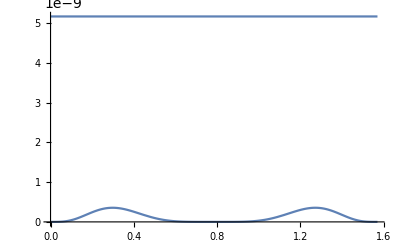

```mathematica
RR[x_]=Abs[f[x]-P[x]];
Gr1=Plot[RR[x],{x,0,π/2}];
Gr2=Plot[R,{x,0,π/2}];
Show[Gr1,Gr2,PlotRange->All]
```